```mathematica
Prec=200;
B1={Subscript[B, "1x"],Subscript[B, "1y"],Subscript[B, "1z"]};
B0={Subscript[B, "0x"],Subscript[B, "0y"],Subscript[B, "0z"]};
v1={Subscript[v, "1x"],Subscript[v, "1y"],Subscript[v, "1z"]};
kvec={k,l,m};
w0=Subscript[ω, 0];
(*w=ω;*)
rho0 = Subscript[ρ, 0];
rho1 = Subscript[ρ, 1];
p0 =Subscript[p, 0];
p1 =Subscript[p, 1];
statevec =Join[{rho1},v1,B1,{p1}];
dw0dp = "∂_p ω_0";
dw0drho = "∂_ρ ω_0";
B0={Subscript[B, "0x"],0,0};
(*B0={0,0,Subscript[B, "0z"]};*)
(*B0={0,Subscript[B, "0y"], Subscript[B, "0z"]};*)
(*B0 = {0,0,0};*)
B0={Subscript[B, "0x"],0,Subscript[B, "0z"]};
(*B0={Subscript[B, "0x"],Subscript[B, "0y"], Subscript[B, "0z"]};*)
σ={B0[[1]]^2/w0,B0[[2]]^2/w0, B0[[3]]^2/w0};
vA={√(σ[[1]]/(1+σ[[1]]+σ[[2]]+σ[[3]])),√(σ[[2]]/(1+σ[[1]]+σ[[2]]+σ[[3]])),√(σ[[3]]/(1+σ[[1]]+σ[[2]]+σ[[3]]))} //Simplify;
vA2 = {Subscript[v, "A,x"]^2==vA[[1]]^2,Subscript[v, "A,y"]^2==vA[[2]]^2,Subscript[v, "A,z"]^2==vA[[3]]^2};
cs2=Subscript[c, s]^2== (w0-dw0drho rho0)/(dw0dp-1)1/w0;
binv = {Subscript[B, "0x"]->(Subscript[v, "A,x"] √Subscript[ω, 0])/(√(1-Subscript[v, "A,x"]^2-Subscript[v, "A,y"]^2-Subscript[v, "A,z"]^2)),Subscript[B, "0y"]->(Subscript[v, "A,y"] √Subscript[ω, 0])/(√(1-Subscript[v, "A,x"]^2-Subscript[v, "A,y"]^2-Subscript[v, "A,z"]^2)),Subscript[B, "0z"]->(Subscript[v, "A,z"] √Subscript[ω, 0])/(√(1-Subscript[v, "A,x"]^2-Subscript[v, "A,y"]^2-Subscript[v, "A,z"]^2))};
zeroBMap={Subscript[v, "A,x"]->0, Subscript[v, "A,y"]->0,Subscript[v, "A,z"]->0, Subscript[B, "0x"]->0,Subscript[B, "0y"]->0,Subscript[B, "0z"]->0,Subscript[B, "1x"]->0,Subscript[B, "1y"]->0,Subscript[B, "1z"]->0};
transformP=Join[{w->γ(w-k Subscript[β, sh]),k->γ(k-w Subscript[β, sh])},zeroBMap];
transformM={w->w,k->k};
ptotP =Subscript[p, t]==Subscript[p, 1];
ptotM =Subscript[p, t] ==Subscript[p, 1]+(B0*B1)[[1]]+(B0*B1)[[2]]+(B0*B1)[[3]];

getvAParam[B0_,vA2_]:=Module[
{B0Trim,vA2Trim,B0invA,f, B0invDef},
B0Trim = Extract[B0,SparseArray[B0]["NonzeroPositions"]];
vA2Trim=Extract[vA2,SparseArray[B0]["NonzeroPositions"]];
B0invA=Sqrt[(B0Trim/.Solve[vA2Trim,B0Trim][[1]])^2];
f[x_]:=x[[1]]->x[[2]];
B0invDef=f /@Transpose[{B0Trim,B0invA}];
{B0Trim,vA2Trim,B0invDef}
];
{B0Trim, vA2Trim, B0invDef} = getvAParam[B0,vA2];
getvfmMap[B0_,kvec_,kk_,ll_,mm_]:=Module[
{kdotb,vA2Symbol,vAtot2,μ,vfm2,vfmMap,kvecMap},
kdotb=0;
vASymbol = {Subscript[v, "A,x"],Subscript[v, "A,y"],Subscript[v, "A,z"]};
vAtot=Simplify[Norm[Extract[vASymbol,SparseArray[B0]["NonzeroPositions"]]],{Subscript[v, "A,x"]>0,Subscript[v, "A,y"]>0,Subscript[v, "A,z"]>0}];
vAtot2=vAtot^2;
μ= Subscript[c, s]^2+ vAtot2-Subscript[c, s]^2 vAtot2+Subscript[c, s]^2 vAtot2 kdotb^2;
vfm2 = (1/2 μ+1/2 √(μ^2-4 Subscript[c, s]^2 vAtot2 kdotb^2))/.Subscript[v, "A,x"]-> vin/.Subscript[v, "A,z"]->vout/.Subscript[c, s]->cs;
(*vfmMap =w->Simplify[√vfm2 * √(k^2+l^2+m^2) * ϕ ,{k>0,l>0,m>0}];*)
vfmMap =w->Simplify[√vfm2 * k * ϕ ,{k>0,l>0,m>0}];
(*kvecMap = {k->kk,l->ll,m->mm};*)
kvecMap = {l->ll};
{vfm2/.kvecMap,vfmMap/.kvecMap}
(*{vfm2/.kvecMap,vfmMap/.l->0}*)
]
vAMap={Subscript[v, "A,x"]->(β ζ)/(√(mr^2+β^2-mr^2 β^2))};
{vfm2,vfmMap}=getvfmMap[B0,kvec,1,0,0];

beta2gamma=Subscript[β, sh]->(√(-1+γ^2))/γ;
```

{k,l,m}

```mathematica
getCharaPoly[w_, w0_, B0_,B1_,v1_,kvec_, statevec_, rho0_,rho1_,dw0dp_,dw0drho_,p1_,cs2_, B0invDef_,vA2Trim_]:=Module[
{continuity,continuityCoeff,  momentum,momentumCoeffx,momentumCoeffy,momentumCoeffz, faraday,faradayCoeffx,faradayCoeffy,faradayCoeffz,energy, energyCoeff, mMatrix, mMatrixForm, detM, characterPoly ,w0Map},
continuity = -w rho1 + Dot[rho0 kvec,v1];
continuityCoeff=Coefficient[continuity,statevec];
momentum = -w w0 v1 +kvec p1 -Cross[Cross[kvec,B1]-Cross[w v1,B0],B0];
momentumCoeffx=Coefficient[momentum[[1]],statevec];
momentumCoeffy=Coefficient[momentum[[2]],statevec];
momentumCoeffz=Coefficient[momentum[[3]],statevec];
faraday = w B1 + Cross[kvec, Cross[v1,B0]];
faradayCoeffx=Coefficient[faraday[[1]], statevec];
faradayCoeffy=Coefficient[faraday[[2]], statevec];
faradayCoeffz=Coefficient[faraday[[3]], statevec];
energy = -w ((dw0dp - 1)p1 + dw0drho rho1) + w0 Dot[kvec,v1];
energyCoeff=Coefficient[energy,statevec];
mMatrix = {continuityCoeff,momentumCoeffx,momentumCoeffy,momentumCoeffz,faradayCoeffx,faradayCoeffy,faradayCoeffz, energyCoeff};
mMatrixForm = mMatrix//MatrixForm;
detM =Det[mMatrix] // Simplify;
w0Map = Solve[cs2,w0][[1]];
characterPoly=detM==0 /.B0invDef/.w0Map ;
{continuity, momentum, faraday,characterPoly,detM}
];

getlPluslMinus2[characterPoly_,transformP_,transformM_]:=Module[
{detMagsonic,detMPlus, detMMinus,l2Plus,l2Minus,l2Ratio},
detMagsonic= characterPoly[[1]]/(w (w^2-k^2 Subscript[v, "A,x"]^2-2 k m Subscript[v, "A,x"] Subscript[v, "A,z"]-m^2 Subscript[v, "A,z"]^2));
detMPlus = Simplify[detMagsonic==0 /.transformP /.Subscript[c, s]->Subscript[c, sw] ];
detMMinus = Simplify[detMagsonic==0 /.transformM/.Subscript[c, s]->Subscript[c, sj]];
l2Plus = l2/.Solve[detMPlus/.l^2->l2,l2]//Simplify;
l2Minus = l2/.Solve[detMMinus/.l^2->l2,l2]//Simplify;
l2Ratio=l2Plus/ l2Minus//Simplify;
{l2Ratio,l2Plus,l2Minus}
];



getlPluslMinus[Faraday_,Momentum_, transformP_, transformM_, B0invDef_,ptotP_,ptotM_]:=Module[
{eqn1,eqn2, eqnPlus, eqnMinus,l1Plus,l1Minus, l1Ratio},
eqn1=Eliminate[{Faraday[[1]]==0,Faraday[[2]]==0,Faraday[[3]]==0,Momentum[[1]]==0,Momentum[[2]]==0,Momentum[[3]]==0, ptotP},{Subscript[p, 1],Subscript[B, "1x"],Subscript[B, "1y"],Subscript[B, "1z"],Subscript[v, "1x"],Subscript[v, "1z"]}];
eqn2=Eliminate[{Faraday[[1]]==0,Faraday[[2]]==0,Faraday[[3]]==0,Momentum[[1]]==0,Momentum[[2]]==0,Momentum[[3]]==0, ptotM},{Subscript[p, 1],Subscript[B, "1x"],Subscript[B, "1y"],Subscript[B, "1z"],Subscript[v, "1x"],Subscript[v, "1z"]}];
eqnPlus =Simplify[eqn1 /.Subscript[ω, 0]->Subscript[ω, "0w"]/. transformP /.B0invDef /. {Subscript[v, "1y"]->Subscript[v, "1y+"],l->SubPlus[l]},{1-Subscript[v, "A,x"]^2-Subscript[v, "A,z"]^2>0,Subscript[v, "A,x"]>0,Subscript[v, "A,z"]>0}];
eqnMinus = Simplify[eqn2/.Subscript[ω, 0]->Subscript[ω, "0j"] /.transformM /.B0invDef/. {Subscript[v, "1y"]->Subscript[v, "1y-"],l->SubMinus[l]},{1-Subscript[v, "A,x"]^2-Subscript[v, "A,z"]^2>0,Subscript[v, "A,x"]>0,Subscript[v, "A,z"]>0}];
l1Plus=SubPlus[l]/.Solve[eqnPlus,SubPlus[l]];
l1Minus=SubMinus[l]/.Solve[eqnMinus,SubMinus[l]];
(*l1Plus/l1Minus /.Subscript[v, "1y+"]->Subscript[v, "1y-"] (w-k Subscript[β, sh])/(w+k Subscript[β, sh])//Simplify*)
l1Ratio=l1Plus/l1Minus /.Subscript[v, "1y+"]->Subscript[v, "1y-"] (γ(w-k Subscript[β, sh]))/w//Simplify;
{l1Ratio,l1Plus, l1Minus}
];
reparametrize[l2_,l_,vfmMap_]:=Module[
{fn1,fn2, lPluslMinus2Phi, lPluslMinusPhi, l2fn, lfn, reMap},
reMap = {Subscript[v, "A,x"]->vin, Subscript[v, "A,z"]->vout, γ->1/(√(1-β^2)), Subscript[β, sh]->β, m->f k, Subscript[c, s]->cs};
lPluslMinus2Phi = l2 /.vfmMap /.reMap;
lPluslMinusPhi = l/.vfmMap /.reMap;
{lPluslMinus2Phi,lPluslMinusPhi}
]
AnthonyMapFn[lPluslMinus2_, lPluslMinus_,tau_]:=Module[
{temp1,temp2,temp3,temp4,poly,paramMap, sommerPlus, sommerMinus, sommerPlus2, sommerMinus2},
temp1=Factor[lPluslMinus2==lPluslMinus^2/.w0W2v/.Subscript[c, sj]->0]/.cosΦMap;
temp2=Factor[temp1/.vMap/.kMap/.w->ϕ*q*v/.gamma2beta/.Subscript[β, sh]->M*v/.Subscript[c, sw]->ϵ*v/.v->η/.τ->tau];
poly=Simplify[Numerator[temp2[[1]]]*Denominator[temp2[[2]]]/ϵ^2/(-1+M η)/(1+M η)==Numerator[temp2[[2]]]*Denominator[temp2[[1]]]/ϵ^2/(-1+M η) /(1+M η)];
paramMap={η->v,ϵ->Subscript[c, sw]/v,M->Subscript[β, sh]/v,ϕ->w/q/v};
temp3=Simplify[Factor[lPluslMinus2/.w0W2v/.Subscript[c, sj]->0]/.cosΦMap/.vMap/.kMap/.w->ϕ*q*v/.gamma2beta/.Subscript[β, sh]->M*v/.Subscript[c, sw]->ϵ*v/.v->η/.τ->tau];
temp4=Simplify[Factor[lPluslMinus/.w0W2v/.Subscript[c, sj]->0]/.cosΦMap/.vMap/.kMap/.w->ϕ*q*v/.gamma2beta/.Subscript[β, sh]->M*v/.Subscript[c, sw]->ϵ*v/.v->η/.τ->tau];
sommerPlus2=Numerator[temp3];
sommerMinus2=Denominator[temp3];
sommerPlus=Numerator[temp4];
sommerMinus=Denominator[temp4];
{poly,paramMap, sommerPlus2, sommerMinus2,sommerPlus, sommerMinus}
]

blandfordMapFn[lPluslMinus2_,lPluslMinus_]:=Module[
{temp1,temp2,temp3,temp4,temp5,paramMap,poly},
temp1=Factor[lPluslMinus2==lPluslMinus^2/.zeroBMap/.kMap/.w->ϕ*q*Subscript[c, sw]/.τ->M*Subscript[c, sw]/Subscript[β, sh]/.Subscript[ω, "0w"]->δ*Subscript[ω, "0j"]*ϵ^2/.Subscript[c, sj]->ϵ*Subscript[c, sw]/.Subscript[c, sw]->η/.beta2gamma];
temp2=Simplify[temp1,{T==ϕ-M,Q==ϕ^2-ϵ^2}];
temp3=Numerator[temp2[[1]]]*Denominator[temp2[[2]]]==Denominator[temp2[[1]]]*Numerator[temp2[[2]]];
temp4=temp3/.{T->ϕ-M,Q->ϕ^2-ϵ^2};
paramMap={η->Subscript[c, sw],M->Subscript[β, sh]*τ/Subscript[c, sw],δ->w0W2w0J[[2]]/Subscript[ω, "0j"]*Subscript[c, sw]^2/Subscript[c, sj]^2/.v->0,γ->1/√(1-Subscript[β, sh]^2)};
poly=Simplify[DivideSides[temp4,ϵ^2],ϵ>0];
temp5=Factor[lPluslMinus/.zeroBMap/.kMap/.w->ϕ*q*Subscript[c, sw]/.τ->M*Subscript[c, sw]/Subscript[β, sh]/.Subscript[ω, "0w"]->δ*Subscript[ω, "0j"]*ϵ^2/.Subscript[c, sj]->ϵ*Subscript[c, sw]/.Subscript[c, sw]->η/.beta2gamma];
sommerPlus=Numerator[temp5];
sommerMinus=Denominator[temp5];
{poly,paramMap,sommerPlus,sommerMinus}
]

vcsMapFn[eqn_]:=Module[
{temp1,temp2,temp3},
tem1=Factor[eqn/.vMap/.gamma2beta/.kMap/.w->ϕ*q*Subscript[c, sw]/.w0W2w0J]
]

mapping[B0_]:=Module[
{kMap,vMap,csw,csj,h0W,w0WMap,w0JMap,h0J,θw2csw,hw2csw,θj2csj,hj2csj,pw,pj,pbalance,pbMap,vA2csw,gamma2beta,w0W2w0J, cosΦMap,w0w2cs,w0j2cs,chi2v,w0W2v},
kMap={k->τ*q,m->q*√(1-τ^2)};
vMap ={Subscript[v, "A,x"]->v*α, Subscript[v, "A,z"]->v √(1-α^2)};
cosΦMap={k*Subscript[v, "A,x"]+m*Subscript[v, "A,z"]->cosΦ * q*v};
gamma2beta=γ->1/√(1-Subscript[β, sh]^2);
w0WMap={Subscript[ω, "0w"]->Subscript[ρ, "0w"]*Subscript[h, "0w"]};
w0JMap={Subscript[ω, "0j"]->Subscript[ρ, "0j"]*Subscript[h, "0j"]};
csw=√((Subscript[Γ, "0w"] Subscript[p, "0w"])/Subscript[ω, "0w"]);
h0W=1+Subscript[θ, "0w"] Subscript[Γ, "0w"]/(Subscript[Γ, "0w"]-1);
csj=√((Subscript[Γ, "0j"] Subscript[p, "0j"])/Subscript[ω, "0j"]);
h0J=1+Subscript[θ, "0j"] Subscript[Γ, "0j"]/(Subscript[Γ, "0j"]-1);

θw2csw=Solve[Subscript[c, sw]==Factor[csw/.w0WMap/.Subscript[h, "0w"]->h0W/.Subscript[p, "0w"]->Subscript[θ, "0w"]*Subscript[ρ, "0w"]],Subscript[θ, "0w"]][[1]][[1]];
hw2csw= Subscript[h, "0w"]->Factor[h0W/.θw2csw];
θj2csj=Solve[Factor[Subscript[c, sj]==csj/.w0JMap/.Subscript[h, "0j"]->h0J/.Subscript[p, "0j"]->Subscript[θ, "0j"]*Subscript[ρ, "0j"]],Subscript[θ, "0j"]][[1]][[1]];
hj2csj= Subscript[h, "0j"]->Factor[h0J/.θj2csj];
w0w2cs=w0WMap/.hw2csw;
w0j2cs=w0JMap/.hj2csj;
pw=Subscript[p, "0w"]/.Solve[Subscript[c, sw]==csw,Subscript[p, "0w"]];
pj=Subscript[p, "0j"]/.Solve[Subscript[c, sj]==csj,Subscript[p, "0j"]];
pbalance=pj[[1]]+Dot[B0,B0]/2==pw[[1]];
w0W2v=Solve[Simplify[pbalance/.B0invDef/.vMap/.Subscript[ω, 0]->Subscript[ω, "0j"]],Subscript[ω, "0w"]][[1]][[1]];
w0W2w0J=Factor[Solve[pbalance,Subscript[ω, "0w"]][[1]][[1]]/.B0invDef/.Subscript[ω, 0]->Subscript[ω, "0j"]/.vMap];
pbMap = Simplify[Factor[pbalance/.newBMap/.vMap/.Subscript[h, "0w"]->h0W/.θw2csw/.Subscript[ρ, "0w"]->χ*Subscript[ρ, "0j"]],Subscript[ρ, "0j"]>0];
vA2csw=Simplify[Solve[Simplify[pbalance/.B0invDef/.vMap]/.Subscript[ω, 0]->Subscript[ω, "0j"]/.w0w2cs/.w0j2cs/.Subscript[ρ, "0w"]->χ*Subscript[ρ, "0j"]/.v^2->v2,v2][[1]][[1]]/.v2->v^2];
chi2v=Solve[v^2==vA2csw[[2]],χ][[1]][[1]];
{Subscript[c, sw]->csw,Subscript[c, sj]->csj,Subscript[h, "0w"]->h0W,θw2csw,hw2csw,pbalance,vA2csw,kMap,vMap,gamma2beta,w0W2w0J,cosΦMap,w0w2cs,w0j2cs,chi2v,w0W2v}
]
{cswMap,csjMap,hw2θw,θw2csw,hw2csw,pbalance,vA2csw,kMap,vMap,gamma2beta,w0W2w0J,cosΦMap,w0w2cs,w0j2cs,chi2v,w0W2v}=mapping[B0]
```

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

General::stop: Further output of Solve::nongen will be suppressed during this calculation.

ReplaceAll::reps: {newBMap} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

{c_sw→√((p_(0w) Γ_(0w))/(ω_(0w))),c_sj→√((p_(0j) Γ_(0j))/(ω_(0j))),h_(0w)→1+(Γ_(0w) θ_(0w))/(-1+Γ_(0w)),θ_(0w)→(-c_sw^2+c_sw^2 Γ_(0w))/(Γ_(0w) (-1-c_sw^2+Γ_(0w))),h_(0w)→(-1+Γ_(0w))/(-1-c_sw^2+Γ_(0w)),1/2 (B_(0x)^2+B_(0z)^2)+(c_sj^2 ω_(0j))/(Γ_(0j))==(c_sw^2 ω_(0w))/(Γ_(0w)),v^2→(2 (c_sj^2 (-1+Γ_(0j)) (-1+Γ_(0w)) Γ_(0w)+c_sw^2 (c_sj^2 Γ_(0w)+Γ_(0j)^2 (χ-χ Γ_(0w))+Γ_(0j) (χ (-1+Γ_(0w))+c_sj^2 (-χ+(-1+χ) Γ_(0w))))))/((2 c_sj^2-Γ_(0j)) (-1+Γ_(0j)) (-1+Γ_(0w)) Γ_(0w)+c_sw^2 (2 c_sj^2 Γ_(0w)+Γ_(0j)^2 (2 χ+(1-2 χ) Γ_(0w))+Γ_(0j) (-2 χ+(-1+2 χ) Γ_(0w)+2 c_sj^2 (-χ+(-1+χ) Γ_(0w))))),{k→q τ,m→q √(1-τ^2)},{v_(A,x)→v α,v_(A,z)→v √(1-α^2)},γ→1/(√(1-β_sh^2)),ω_(0w)→-((2 c_sj^2-2 v^2 c_sj^2+v^2 Γ_(0j)) Γ_(0w) ω_(0j))/(2 (-1+v) (1+v) c_sw^2 Γ_(0j)),{k v_(A,x)+m v_(A,z)→cosΦ q v},{ω_(0w)→((-1+Γ_(0w)) ρ_(0w))/(-1-c_sw^2+Γ_(0w))},{ω_(0j)→((-1+Γ_(0j)) ρ_(0j))/(-1-c_sj^2+Γ_(0j))},χ→-((-1+Γ_(0j)) (2 c_sj^2-2 v^2 c_sj^2+v^2 Γ_(0j)) Γ_(0w) (-1-c_sw^2+Γ_(0w)))/(2 (-1+v^2) c_sw^2 Γ_(0j) (-1-c_sj^2+Γ_(0j)) (-1+Γ_(0w))),ω_(0w)→-((2 c_sj^2-2 v^2 c_sj^2+v^2 Γ_(0j)) Γ_(0w) ω_(0j))/(2 (-1+v^2) c_sw^2 Γ_(0j))}

```mathematica
{continuity, momentum, faraday,poly1,detM}=getCharaPoly[w,w0,B0,B1,v1,kvec,statevec, rho0,rho1, dw0dp, dw0drho,p1,cs2, B0invDef,vA2Trim];
poly2=Simplify[poly1,w0>0 && -1+Subscript[v, "A,x"]^2+Subscript[v, "A,y"]^2+Subscript[v, "A,z"]^2<0 && Subscript[v, "A,x"]>0 && Subscript[v, "A,y"]>0&&Subscript[v, "A,z"]>0] ;
characterPoly=Eliminate[{poly2,cs2},{w0,rho0}][[1]]//Simplify
```

w (w^2-k^2 v_(A,x)^2-2 k m v_(A,x) v_(A,z)-m^2 v_(A,z)^2) (w^2 (w^2-(k^2+l^2+m^2) v_(A,x)^2-(k^2+l^2+m^2) v_(A,z)^2)+c_s^2 (-((k^2+l^2+m^2) w^2)+(k^4+k^2 (l^2+m^2)+(l^2+m^2) w^2) v_(A,x)^2+2 k m (k^2+l^2+m^2-w^2) v_(A,x) v_(A,z)+(m^4+k^2 (m^2+w^2)+l^2 (m^2+w^2)) v_(A,z)^2))==0

```mathematica
{lPluslMinus2,l2Plus,l2Minus}=getlPluslMinus2[characterPoly, transformP, transformM]
```

{{((-w^2 (v_(A,x)^2+v_(A,z)^2)+c_sj^2 (-w^2+(k^2+w^2) v_(A,x)^2+2 k m v_(A,x) v_(A,z)+(m^2+w^2) v_(A,z)^2)) (-m^2-k^2 γ^2+2 k w γ^2 β_sh-w^2 γ^2 β_sh^2+(γ^2 (w-k β_sh)^2)/c_sw^2))/(w^2 (-w^2+(k^2+m^2) v_(A,x)^2+(k^2+m^2) v_(A,z)^2)-c_sj^2 (-((k^2+m^2) w^2)+(k^4+k^2 m^2+m^2 w^2) v_(A,x)^2+2 k m (k^2+m^2-w^2) v_(A,x) v_(A,z)+(m^4+k^2 (m^2+w^2)) v_(A,z)^2))},{-m^2-k^2 γ^2+2 k w γ^2 β_sh-w^2 γ^2 β_sh^2+(γ^2 (w-k β_sh)^2)/c_sw^2},{(w^2 (-w^2+(k^2+m^2) v_(A,x)^2+(k^2+m^2) v_(A,z)^2)-c_sj^2 (-((k^2+m^2) w^2)+(k^4+k^2 m^2+m^2 w^2) v_(A,x)^2+2 k m (k^2+m^2-w^2) v_(A,x) v_(A,z)+(m^4+k^2 (m^2+w^2)) v_(A,z)^2))/(-w^2 (v_(A,x)^2+v_(A,z)^2)+c_sj^2 (-w^2+(k^2+w^2) v_(A,x)^2+2 k m v_(A,x) v_(A,z)+(m^2+w^2) v_(A,z)^2))}}

```mathematica
{lPluslMinus, lPlus, lMinus}=getlPluslMinus[faraday,momentum,transformP, transformM, B0invDef/.Subscript[ω, 0]->Subscript[ω, "0j"],ptotP,ptotM]
```

{{-(γ^2 (-1+v_(A,x)^2+v_(A,z)^2) (w-k β_sh)^2 ω_(0w))/((w^2-k^2 v_(A,x)^2-2 k m v_(A,x) v_(A,z)-m^2 v_(A,z)^2) ω_(0j))},{(γ v_(1y+) (w-k β_sh) ω_(0w))/p_t},{-(v_(1y-) (w^2-k^2 v_(A,x)^2-2 k m v_(A,x) v_(A,z)-m^2 v_(A,z)^2) ω_(0j))/(w p_t (-1+v_(A,x)^2+v_(A,z)^2))}}

```mathematica
asymDMFn[lPluslMinus2_,lPluslMinus_,l2Plus_,l2Minus_,lPlus_,lMinus_]:=Module[
{lPlM2,lPlM,eqn1,eqn2,somP2,somM2,somP,somM,arglPlM,arglPlM2},
lPlM2=Simplify[Simplify[lPluslMinus2/.Subscript[c, sj]->0,R==k^2+m^2]/.vMap,{Q==(k-w Subscript[β, sh])^2,T==(w-k Subscript[β, sh])^2}]/.Q->(k-w Subscript[β, sh])^2/.T->(w-k Subscript[β, sh])^2/.R->k^2+m^2;
lPlM=Simplify[Simplify[lPluslMinus,S==k Subscript[v, "A,x"]+m Subscript[v, "A,z"]]/.vMap]/.S->k Subscript[v, "A,x"]+m Subscript[v, "A,z"];
arglPlM2=Simplify[lPlM2/.kMap/.w->ϕ*q*v/.gamma2beta/.Subscript[β, sh]->M*v/.Subscript[c, sw]->ϵ*v/.v->η]/.τ->cosθ;
arglPlM=Simplify[lPlM/.cosΦMap/.kMap/.w->ϕ*q*v/.w0W2v/.Subscript[c, sj]->0/.gamma2beta/.Subscript[β, sh]->M*v/.Subscript[c, sw]->ϵ*v/.v->η]/.τ->cosθ;
somP2=Simplify[l2Plus/.kMap/.w->ϕ*v*q/.gamma2beta/.Subscript[β, sh]->M*v/.Subscript[c, sw]->ϵ*v/.v->η]/.τ->cosθ/.q->1;
somM2=Simplify[l2Minus/.Subscript[c, sj]->0/.vMap/.kMap/.w->ϕ*v*q]/.τ->cosθ/.q->1;
somP=Simplify[lPlus/.Subscript[v, "1y+"]->Subscript[v, "1y-"] (γ(w-k Subscript[β, sh]))/w/.gamma2beta/.kMap/.w->ϕ*v*q/.Subscript[β, sh]->M*v/.τ->cosθ]/.w0W2v/.Subscript[c, sj]->0/.Subscript[c, sw]->ϵ*v/.{q->1,Subscript[v, "1y-"]->1,Subscript[p, t]->1,Subscript[ω, "0j"]->1}/.v->η;
somM=Simplify[lMinus/.-k^2 Subscript[v, "A,x"]^2-2 k m Subscript[v, "A,x"] Subscript[v, "A,z"]-m^2 Subscript[v, "A,z"]^2->Simplify[-k^2 Subscript[v, "A,x"]^2-2 k m Subscript[v, "A,x"] Subscript[v, "A,z"]-m^2 Subscript[v, "A,z"]^2]/.cosΦMap/.vMap/.w->ϕ*v*q/.Subscript[β, sh]->M*v/.τ->cosθ]/.{q->1,Subscript[v, "1y-"]->1,Subscript[p, t]->1,Subscript[ω, "0j"]->1}/.v->η;
eqn1=arglPlM2*ϵ^2 (-1+M^2 η^2)==arglPlM^2*ϵ^2 (-1+M^2 η^2);
eqn2=Numerator[eqn1[[1]]]*Denominator[eqn1[[2]]]==Numerator[eqn1[[2]]]*Denominator[eqn1[[1]]];
{eqn2,somP2,somM2,somP,somM, arglPlM2,arglPlM,lPlM2,lPlM}
]
```

```mathematica
{dm,somP2,somM2,somP, somM,arglPlM2,arglPlM,lPlM2,lPlM}=asymDMFn[lPluslMinus2[[1]],lPluslMinus[[1]],l2Plus[[1]],l2Minus[[1]],lPlus[[1]],lMinus[[1]]]
```

{4 ϵ^2 (-1+M^2 η^2) (cosΦ^2-ϕ^2)^2 (-(-cosθ M+ϕ)^2+ϵ^2 (1-2 cosθ M η^2 ϕ+M^2 η^2 (-1+cosθ^2+η^2 ϕ^2)))==(-cosθ M+ϕ)^4 (-1+ϕ^2) Γ_(0w)^2,(-(-cosθ M+ϕ)^2+ϵ^2 (1-2 cosθ M η^2 ϕ+M^2 η^2 (-1+cosθ^2+η^2 ϕ^2)))/(ϵ^2 (-1+M^2 η^2)),-1+ϕ^2,(η (-cosθ M+ϕ)^2 Γ_(0w))/(2 ϵ^2 (-1+η^2) (-1+M^2 η^2) ϕ),(η (cosΦ^2-ϕ^2))/((-1+η^2) ϕ),(-(-cosθ M+ϕ)^2+ϵ^2 (1-2 cosθ M η^2 ϕ+M^2 η^2 (-1+cosθ^2+η^2 ϕ^2)))/(ϵ^2 (-1+M^2 η^2) (-1+ϕ^2)),((-cosθ M+ϕ)^2 Γ_(0w))/(2 ϵ^2 (-1+M^2 η^2) (cosΦ^2-ϕ^2)),(v^2 (-γ^2 (w-k β_sh)^2+c_sw^2 (m^2+γ^2 (k-w β_sh)^2)))/(((k^2+m^2) v^2-w^2) c_sw^2),((-1+v^2) γ^2 (w-k β_sh)^2 ω_(0w))/((-w^2+(k v_(A,x)+m v_(A,z))^2) ω_(0j))}

```mathematica
dmFullFn[MMe0_, costheta0_]:=Module[
{soln,eqn,epsilon,phi2,phi3,phi4,phi5,phi6,MM,sP,sM,physSoln, MMe, costheta},
{MMe,costheta}=SetPrecision[{MMe0,costheta0},50];
epsilon=csw/eta;
MM=MMe/costheta;
eqn=ϕ/.NSolve[dm/.{η->eta, cosΦ->cosphi, ϵ->epsilon, Subscript[Γ, "0w"]->5/3, M->MM,cosθ->costheta},ϕ,WorkingPrecision->50];
sP=somP/.{η->eta, cosΦ->cosphi, ϵ->epsilon, Subscript[Γ, "0w"]->5/3, M->MM,cosθ->costheta}/.ϕ->eqn;
sM=somM/.{η->eta, cosΦ->cosphi, ϵ->epsilon, Subscript[Γ, "0w"]->5/3, M->MM,cosθ->costheta}/.ϕ->eqn;
flag1=Boole[Map[Im[#]<0 &,sP]];
flag2=Boole[Map[Im[#]>0 &,sM]];
physSoln=flag1*flag2;
phi2=Max[Im[eqn]*physSoln,0]/.Indeterminate->0;
phi4=phi2*If[MM*eta<1,1,0];
phi5=phi4*If[MMe<0.98|| MMe>1.02,1,0];
phi4
];
```

```mathematica
csw=0.005;
cosphi=0;
res=50;
memax=2;
eta=0.2;
eta1=eta
dat1=Table[dmFullFn[x,y],{y,0.00001,1,1/res},{x,0.00001,memax,memax/res}];
maxdat1=Max[dat1];
eta=0.5;
eta2=eta
dat2=Table[dmFullFn[x,y],{y,0.00001,1,1/res},{x,0.00001,memax,memax/res}];
maxdat2=Max[dat2];
eta=0.8;
eta3=eta
dat3=Table[dmFullFn[x,y],{y,0.00001,1,1/res},{x,0.00001,memax,memax/res}];
maxdat3=Max[dat3];
```

0.2

NSolve::precw: The precision of the argument function ({-25/9 (-0.00001000000000000000081803053914031309545862313825637+ϕ)^4 (-1+ϕ^2)-0.0024 ϕ^4 (-(-«97»+ϕ)^2+0.000625 (1-8.×10^-7 ϕ+0.04 Plus[«2»]))}) is less than WorkingPrecision (50).

NSolve::precw: The precision of the argument function ({-25/9 (-0.0400100000000000038946623703850491438060998916626+ϕ)^4 (-1+ϕ^2)+1600.8 ϕ^4 (-(-«97»+ϕ)^2+0.000625 (1-0.0032008 ϕ+640320. Plus[«2»]))}) is less than WorkingPrecision (50).

NSolve::precw: The precision of the argument function ({-25/9 (-0.08000999999999999778843573494668817147612571716309+ϕ)^4 (-1+ϕ^2)+6401.6 ϕ^4 (-(-«97»+ϕ)^2+0.000625 (1-0.0064008 ϕ+2.56064×10^6 Plus[«2»]))}) is less than WorkingPrecision (50).

General::stop: Further output of NSolve::precw will be suppressed during this calculation.

0.5

NSolve::precw: The precision of the argument function ({-25/9 (-0.00001000000000000000081803053914031309545862313825637+ϕ)^4 (-1+ϕ^2)-0.0003 ϕ^4 (-(-«97»+ϕ)^2+0.0001 (1-5.×10^-6 ϕ+0.25 Plus[«2»]))}) is less than WorkingPrecision (50).

NSolve::precw: The precision of the argument function ({-25/9 (-0.0400100000000000038946623703850491438060998916626+ϕ)^4 (-1+ϕ^2)+1600.8 ϕ^4 (-(-«97»+ϕ)^2+0.0001 (1-0.020005 ϕ+4.002×10^6 Plus[«2»]))}) is less than WorkingPrecision (50).

NSolve::precw: The precision of the argument function ({-25/9 (-0.08000999999999999778843573494668817147612571716309+ϕ)^4 (-1+ϕ^2)+6401.6 ϕ^4 (-(-«97»+ϕ)^2+0.0001 (1-0.040005 ϕ+1.6004×10^7 Plus[«2»]))}) is less than WorkingPrecision (50).

General::stop: Further output of NSolve::precw will be suppressed during this calculation.

0.8

NSolve::precw: The precision of the argument function ({-25/9 (-0.00001000000000000000081803053914031309545862313825637+ϕ)^4 (-1+ϕ^2)-0.00005625 ϕ^4 (-(-«97»+ϕ)^2+0.0000390625 (1-0.0000128 ϕ+0.64 Plus[«2»]))}) is less than WorkingPrecision (50).

NSolve::precw: The precision of the argument function ({-25/9 (-0.0400100000000000038946623703850491438060998916626+ϕ)^4 (-1+ϕ^2)+1600.8 ϕ^4 (-(-«97»+ϕ)^2+0.0000390625 (1-0.0512128 ϕ+1.02451×10^7 Plus[«2»]))}) is less than WorkingPrecision (50).

NSolve::precw: The precision of the argument function ({-25/9 (-0.08000999999999999778843573494668817147612571716309+ϕ)^4 (-1+ϕ^2)+6401.6 ϕ^4 (-(-«97»+ϕ)^2+0.0000390625 (1-0.102413 ϕ+4.09702×10^7 Plus[«2»]))}) is less than WorkingPrecision (50).

General::stop: Further output of NSolve::precw will be suppressed during this calculation.

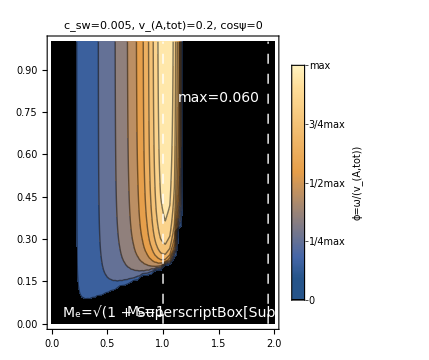
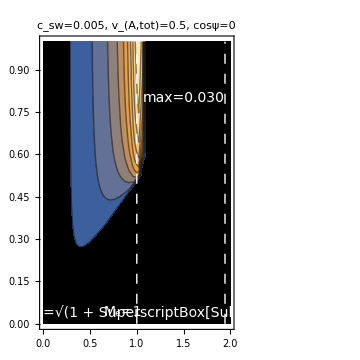
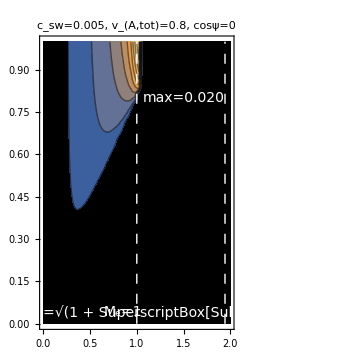
-Graphics--Graphics--Graphics-cosθM_e=β_sh/(v_(A,tot))cosθ

```mathematica
plt1=ListContourPlot[dat1/maxdat1,
ColorFunction->dmColor,
PlotRange->Full,
DataRange->{{0,2},{0,1}},
PlotLabel->Style["c_sw="<>ToString[csw]<>",   v_(<A,tot>)="<>ToString[eta1]<>",  cosψ=" <>ToString[cosphi],20],
Epilog->{Thick,White,Dashing[0.02,0.02],Line[{{1,0},{1,1}}],Thick,White,Line[{{1.94365,0},{1.94365,1}}],Text[Style["M_e=1",FontSize->14],{0.85,0.04}],Text[Style["M_e=√(1 + SuperscriptBox[SubscriptBox[Γ, w], 2])",FontSize->14],{1.65,0.04}],Text[Style["max=" <>ToString[NumberForm[maxdat1,{1,3}]],FontSize->14],{1.5,0.8}]},
FrameTicksStyle->Directive[Automatic,16],
ImageSize->Medium];
plt2=ListContourPlot[dat2/maxdat2,
ColorFunction->dmColor,
PlotRange->Full,
DataRange->{{0,2},{0,1}},
PlotLabel->Style["c_sw="<>ToString[csw]<>",   v_(<A,tot>)="<>ToString[eta2]<>",  cosψ=" <>ToString[cosphi],20],
Epilog->{Thick,White,Dashing[0.02,0.02],Line[{{1,0},{1,1}}],Thick,White,Line[{{1.94365,0},{1.94365,1}}],Text[Style["M_e=1",FontSize->14],{0.85,0.04}],Text[Style["M_e=√(1 + SuperscriptBox[SubscriptBox[Γ, w], 2])",FontSize->14],{1.65,0.04}],Text[Style["max=" <>ToString[NumberForm[maxdat2,{1,3}]],FontSize->14],{1.5,0.8}]},
FrameTicksStyle->Directive[Automatic,16],
ImageSize->Medium];
plt3=ListContourPlot[dat3/maxdat3,
ColorFunction->dmColor,
PlotRange->Full,
DataRange->{{0,2},{0,1}},
PlotLabel->Style["c_sw="<>ToString[csw]<>",   v_(<A,tot>)="<>ToString[eta3]<>",  cosψ=" <>ToString[cosphi],20],
Epilog->{Thick,White,Dashing[0.02,0.02],Line[{{1,0},{1,1}}],Thick,White,Line[{{1.94365,0},{1.94365,1}}],Text[Style["M_e=1",FontSize->14],{0.85,0.04}],Text[Style["M_e=√(1 + SuperscriptBox[SubscriptBox[Γ, w], 2])",FontSize->14],{1.65,0.04}],Text[Style["max=" <>ToString[NumberForm[maxdat3,{1,3}]],FontSize->14],{1.5,0.8}]},
FrameTicksStyle->Directive[Automatic,16],
ImageSize->Medium];
Legended[Labeled[Row[{plt1,plt2,plt3}],
{Pane["cosθ"],"M_e=β_sh/(v_(<A,tot>))cosθ"},{Left,Bottom},
LabelStyle->Directive[Black,20]
], 
Placed[BarLegend[{dmColor[#]&,{0,1}},
"Ticks"->{0,0.25,0.5,0.75,1},"TickLabels"->{0,"1/4max","1/2max","3/4max","max"},
LabelStyle->{FontSize->15},
LegendLayout->"Column",LegendMarkerSize->300, LegendLabel -> "ϕ=ω/(v_(<A,tot>))"],After]]
```

```mathematica
csw=0.005;
cosphi=1;
res=50;
memax=2;
eta=0.2;
eta1=eta
dat1=Table[dmFullFn[x,y],{y,0.00001,1,1/res},{x,0.00001,memax,memax/res}];
maxdat1=Max[dat1];
eta=0.5;
eta2=eta
dat2=Table[dmFullFn[x,y],{y,0.00001,1,1/res},{x,0.00001,memax,memax/res}];
maxdat2=Max[dat2];
eta=0.8;
eta3=eta
dat3=Table[dmFullFn[x,y],{y,0.00001,1,1/res},{x,0.00001,memax,memax/res}];
maxdat3=Max[dat3];
(*Export["/Volumes/Samsung_T5/2ndPhD/full_in_dat1.hdf5",dat1,"HDF5"]
Export["/Volumes/Samsung_T5/2ndPhD/full_in_dat2.hdf5",dat2,"HDF5"]
Export["/Volumes/Samsung_T5/2ndPhD/full_in_dat3.hdf5",dat3,"HDF5"]*)
```

0.2

NSolve::precw: The precision of the argument function ({-25/9 (-0.00001000000000000000081803053914031309545862313825637+ϕ)^4 (-1+ϕ^2)-0.0024 (1-ϕ^2)^2 (-(-0.00001000000000000000081803053914031309545862313825637+ϕ)^2+0.000625 (1-8.×10^-7 ϕ+0.04 Plus[«2»]))}) is less than WorkingPrecision (50).

NSolve::precw: The precision of the argument function ({-25/9 (-0.0400100000000000038946623703850491438060998916626+ϕ)^4 (-1+ϕ^2)+1600.8 (1-ϕ^2)^2 (-(-0.0400100000000000038946623703850491438060998916626+ϕ)^2+0.000625 (1-0.0032008 ϕ+640320. Plus[«2»]))}) is less than WorkingPrecision (50).

NSolve::precw: The precision of the argument function ({-25/9 (-0.08000999999999999778843573494668817147612571716309+ϕ)^4 (-1+ϕ^2)+6401.6 (1-ϕ^2)^2 (-(-0.08000999999999999778843573494668817147612571716309+ϕ)^2+0.000625 (1-0.0064008 ϕ+2.56064×10^6 Plus[«2»]))}) is less than WorkingPrecision (50).

General::stop: Further output of NSolve::precw will be suppressed during this calculation.

0.5

NSolve::precw: The precision of the argument function ({-25/9 (-0.00001000000000000000081803053914031309545862313825637+ϕ)^4 (-1+ϕ^2)-0.0003 (1-ϕ^2)^2 (-(-0.00001000000000000000081803053914031309545862313825637+ϕ)^2+0.0001 (1-5.×10^-6 ϕ+0.25 Plus[«2»]))}) is less than WorkingPrecision (50).

NSolve::precw: The precision of the argument function ({-25/9 (-0.0400100000000000038946623703850491438060998916626+ϕ)^4 (-1+ϕ^2)+1600.8 (1-ϕ^2)^2 (-(-0.0400100000000000038946623703850491438060998916626+ϕ)^2+0.0001 (1-0.020005 ϕ+4.002×10^6 Plus[«2»]))}) is less than WorkingPrecision (50).

NSolve::precw: The precision of the argument function ({-25/9 (-0.08000999999999999778843573494668817147612571716309+ϕ)^4 (-1+ϕ^2)+6401.6 (1-ϕ^2)^2 (-(-0.08000999999999999778843573494668817147612571716309+ϕ)^2+0.0001 (1-0.040005 ϕ+1.6004×10^7 Plus[«2»]))}) is less than WorkingPrecision (50).

General::stop: Further output of NSolve::precw will be suppressed during this calculation.

0.8

NSolve::precw: The precision of the argument function ({-25/9 (-0.00001000000000000000081803053914031309545862313825637+ϕ)^4 (-1+ϕ^2)-0.00005625 (1-ϕ^2)^2 (-(-0.00001000000000000000081803053914031309545862313825637+ϕ)^2+0.0000390625 (1-0.0000128 ϕ+0.64 Plus[«2»]))}) is less than WorkingPrecision (50).

NSolve::precw: The precision of the argument function ({-25/9 (-0.0400100000000000038946623703850491438060998916626+ϕ)^4 (-1+ϕ^2)+1600.8 (1-ϕ^2)^2 (-(-0.0400100000000000038946623703850491438060998916626+ϕ)^2+0.0000390625 (1-0.0512128 ϕ+1.02451×10^7 Plus[«2»]))}) is less than WorkingPrecision (50).

NSolve::precw: The precision of the argument function ({-25/9 (-0.08000999999999999778843573494668817147612571716309+ϕ)^4 (-1+ϕ^2)+6401.6 (1-ϕ^2)^2 (-(-0.08000999999999999778843573494668817147612571716309+ϕ)^2+0.0000390625 (1-0.102413 ϕ+4.09702×10^7 Plus[«2»]))}) is less than WorkingPrecision (50).

General::stop: Further output of NSolve::precw will be suppressed during this calculation.

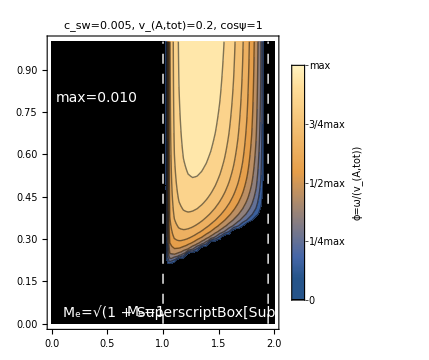
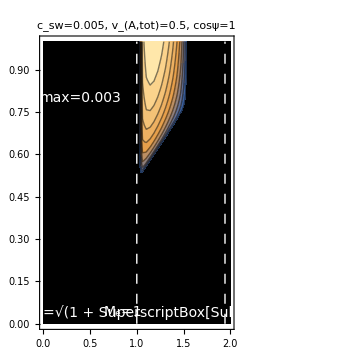
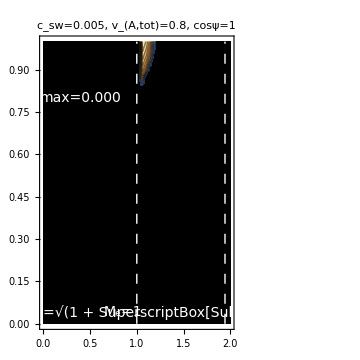
-Graphics--Graphics--Graphics-cosθM_e=β_sh/(v_(A,tot))cosθ

```mathematica
plt1=ListContourPlot[dat1/maxdat1,
ColorFunction->dmColor,
PlotRange->Full,
DataRange->{{0,2},{0,1}},
PlotLabel->Style["c_sw="<>ToString[csw]<>",   v_(<A,tot>)="<>ToString[eta1]<>",  cosψ=" <>ToString[cosphi],20],
Epilog->{Thick,White,Dashing[0.02,0.02],Line[{{1,0},{1,1}}],Thick,White,Line[{{1.94365,0},{1.94365,1}}],Text[Style["M_e=1",FontSize->14],{0.85,0.04}],Text[Style["M_e=√(1 + SuperscriptBox[SubscriptBox[Γ, w], 2])",FontSize->14],{1.65,0.04}],Text[Style["max=" <>ToString[NumberForm[maxdat1,{1,3}]],FontSize->14],{0.4,0.8}]},
FrameTicksStyle->Directive[Automatic,16],
ImageSize->Medium];
plt2=ListContourPlot[dat2/maxdat2,
ColorFunction->dmColor,
PlotRange->Full,
DataRange->{{0,2},{0,1}},
PlotLabel->Style["c_sw="<>ToString[csw]<>",   v_(<A,tot>)="<>ToString[eta2]<>",  cosψ=" <>ToString[cosphi],20],
Epilog->{Thick,White,Dashing[0.02,0.02],Line[{{1,0},{1,1}}],Thick,White,Line[{{1.94365,0},{1.94365,1}}],Text[Style["M_e=1",FontSize->14],{0.85,0.04}],Text[Style["M_e=√(1 + SuperscriptBox[SubscriptBox[Γ, w], 2])",FontSize->14],{1.65,0.04}],Text[Style["max=" <>ToString[NumberForm[maxdat2,{1,3}]],FontSize->14],{0.4,0.8}]},

FrameTicksStyle->Directive[Automatic,16],
ImageSize->Medium];
plt3=ListContourPlot[dat3/maxdat3,
ColorFunction->dmColor,
PlotRange->Full,
DataRange->{{0,2},{0,1}},
PlotLabel->Style["c_sw="<>ToString[csw]<>",   v_(<A,tot>)="<>ToString[eta3]<>",  cosψ=" <>ToString[cosphi],20],
Epilog->{Thick,White,Dashing[0.02,0.02],Line[{{1,0},{1,1}}],Thick,White,Line[{{1.94365,0},{1.94365,1}}],Text[Style["M_e=1",FontSize->14],{0.85,0.04}],Text[Style["M_e=√(1 + SuperscriptBox[SubscriptBox[Γ, w], 2])",FontSize->14],{1.65,0.04}],Text[Style["max=" <>ToString[NumberForm[maxdat3,{1,3}]],FontSize->14],{0.4,0.8}]},

FrameTicksStyle->Directive[Automatic,16],
ImageSize->Medium];
Legended[Labeled[Row[{plt1,plt2,plt3}],
{Pane["cosθ"],"M_e=β_sh/(v_(<A,tot>))cosθ"},{Left,Bottom},
LabelStyle->Directive[Black,20]
], 
Placed[BarLegend[{dmColor[#]&,{0,1}},
"Ticks"->{0,0.25,0.5,0.75,1},"TickLabels"->{0,"1/4max","1/2max","3/4max","max"},
LabelStyle->{FontSize->15},
LegendLayout->"Column",LegendMarkerSize->300, LegendLabel -> "ϕ=ω/(v_(<A,tot>))"],After]]
```